# A discourse language for card games:

#### The structure of the platform design:

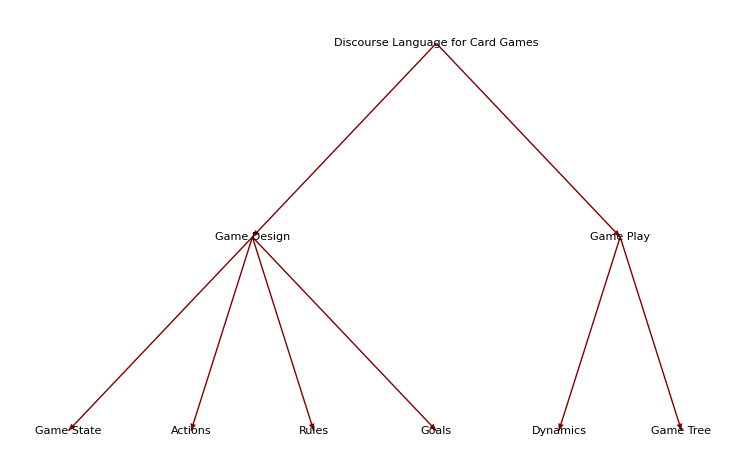

```mathematica
TreePlot[Join[Thread["Discourse Language for Card Games"->{"Game Design", "Game Play"}],Thread["Game Design"->{"Game State", "Actions", "Rules", "Goals"}], Thread["Game Play"-> {"Dynamics", "Game Tree"}]],VertexLabeling->True, ImageSize->750, BaseStyle->{FontSize->20}, DirectedEdges->True]
```

## Game Design

## Environment (gameState)

defining suits and cards:

```mathematica
suits = {"Clubs", "Hearts", "Spades", "Diamonds"};
numbers = {"Ace", 2, 3, 4, 5, 6, 7, 8, 9, 10, "Jack", "Queen", "King"};
cardsList = Outer[List, suits, numbers]//Flatten[#,1]&;
cardImagesList={};
cardImages = AssociationThread[cardsList,ImageResize[#,50]&/@Take[cardImagesList,52]];
```

create an association of “players”, representing who controls the game:

```mathematica
ControlState[players_List] := AssociationThread[players, False];
```

create an association, representing a card deal, in which there are a stack, a stock, and “players”, each having number of “handN” random cards:

```mathematica
CardDeal[players_List, handN_]:= 
Module[{playersN = Length[players], shuffle},
	shuffle = TakeDrop[RandomSample[cardsList], playersN*handN];
	<|AssociationThread[players -> Partition[shuffle[[1]], handN]], "stack" -> Drop[shuffle[[2]],1],"stock"->{shuffle[[2,1]]}|>
];
```

create initial gameState:

```mathematica
CreateGameState[players_List, handsN_]:= Module[{
	controlState = ControlState[players],
	cardDeal = CardDeal[players, handsN]
	},
	controlState[players[[1]]] = True;
	AssociateTo[cardDeal, "controlState" -> controlState]
];
```

gameState visualization in a grid (uses “cardImages”):

```mathematica
VisualizeCardGame[gameState_] := Module[{
	controlNumber = Position[gameState["controlState"]//Values, True][[1,1]],
	handsList = Select[Keys[gameState], ListQ[gameState[#]]&],
	hands
	},
	hands = Values[gameState[[handsList]]];
	Grid[Transpose[{handsList, hands}], Frame -> All, Background -> {None,{controlNumber->LightBlue}}]/.cardImages
];
```

## Actions (gameState changers)

### sub-actions (building blocks for actions):

```mathematica
CardTake[hand_, card_][gameState_Association]:= 
Module[{actualCard=
Piecewise[{ 
{card,
ListQ[card]},
{gameState[hand][[card]],
IntegerQ[card]},
{Last[gameState[hand]],
card=="top"},
{First[gameState[hand]],
card=="bottom"},
{RandomChoice[gameState[hand]],
card=="random"}
}
]},
Hold[{gameState/.gameState[hand]->DeleteCases[gameState[hand],actualCard],actualCard}]
];


CardDrop[hand_][CardTake_CardTake]:= 
Module[{pseudogameState=ReleaseHold[CardTake],gameStatedummy, actualCard},
gameStatedummy=pseudogameState//First;
actualCard=pseudogameState//Last;	
gameStatedummy/.gameStatedummy[hand]->Append[gameStatedummy[hand],actualCard]
];

WhoControls[gameState_]:= 
Module[{controlState=gameState["controlState"]},
First@@(Position[controlState, True]//Flatten)]
```

### actions (change the state of the game):

Move to the next player:

```mathematica
NextPlayer[gameState_] :=  
Module[{controlState=gameState["controlState"]},
gameState/.gameState["controlState"]-> AssociationThread[controlState//Keys, RotateRight[controlState//Values]]];
```

Move “card” from “hand1” to “hand2” by appending:

```mathematica
CardMove[hand1_->hand2_, card_][gameState_] := gameState//CardTake[hand1, card]//CardDrop[hand2];
```

Draws the top card from stack to “player”:

```mathematica
CardDraw[player_][gameState_] := gameState//CardMove["stack"->player, "top"];
```

Move stock cards to stack:

```mathematica
MoveStocktoStack[gameState_] := Module[{
cardlist = Most[gameState["stock"]]},
gameState/.{gameState["stack"]->Join[RandomSample[cardlist], gameState["stack"]],gameState["stock"]->Take[gameState["stock"], -1]}
];
```

## Rules (legal actions in a gameState)

### conditionals (to be used in rules conditions):

```mathematica
SameSuitOrNumberQ[card1_, card2_] := card1[[1]]== card2[[1]]||card1[[2]]== card2[[2]];

PlayerTurnQ[player_][gameState_] := If[MemberQ[playersList, player], 
gameState["controlState", player],
False];

PossibleDropQ[player_][gameState_] := AnyTrue[gameState[player], SameSuitOrNumberQ[#,gameState["stock"]//Last]&];

EmptyStackQ[gameState_] := (gameState["stack"]== {});
```

### rules (legal moves):

list of rules to play the game with:

```mathematica
rules = {rule1, rule2, rule3};
```

if turn and similar card to stock top, then drop:

```mathematica
rule1 = gameState:<|___,player_->{___,card1_,___},___,"stock"->{___,card2_},___|> /;(PlayerTurnQ[player][gameState] && SameSuitOrNumberQ[card1,card2]):> (gameState//CardMove[player->"stock", card1]//NextPlayer);
```

if turn and no similar card to stock top, then draw from stack:

```mathematica
rule2 = gameState:<|___,player_->{___},___|> /;(PlayerTurnQ[player][gameState] && !PossibleDropQ[player][gameState] && !EmptyStackQ[gameState]) :> (gameState//CardDraw[player]//NextPlayer);
```

if stack is empty, shuffle cards in stock and move to stack:

```mathematica
rule3 = gameState:<|___|> /;(EmptyStackQ[gameState]) :> (gameState//MoveStocktoStack);
```

if turn, draw from stack:

```mathematica
rule4 = gameState:<|___,player_->{___},___|> /;(PlayerTurnQ[player][gameState]) :> (gameState//CardDraw[player]//NextPlayer);
```

a new state, played with certain rules, can be generated using:

```mathematica
newgameState = Replace[gameState, {rule1, rule2}];
```

## Goals (end gameState and scores)

end the game (if any player runs out of cards):

```mathematica
EndGameQ[gameState_]:= AnyTrue[gameState/@playersList, (#=={})&];

GameContinueQ[gameState_] := Not[EndGameQ[gameState]];
```

scores (the player with no card gets 1):

```mathematica
Winner[gameState_] := If[
	EndGameQ[gameState],
	Select[playersList, (gameState[#]=={})&]//First,
	False];

Score[player_][gameState_] := If[
	gameState[player]=={},
	1,
	0];
```

## Game Play

## Dynamics

### sub-function:

```mathematica
ReplaceRandom[initialState_, rules_] := RandomChoice[ReplaceList[initialState, rules]];
```

### functions to generate a “playList” (list of game states) in a game play :

generate a list of game states while playing the first move that it finds (using Replace and “ContinueGameQ”):

```mathematica
PlayGameList[initialState_, rules_, maxsteps_] := NestWhileList[Replace[#, rules]&, initialState, GameContinueQ, 1, maxsteps];
```

generate a list of game states while playing randomly, by picking a random move each turn from all possible moves (using “ReplaceRandom” and “ContinueGameQ”) :

```mathematica
PlayRandomList[initialState_, rules_, maxsteps_] := NestWhileList[ReplaceRandom[#, rules]&, initialState, GameContinueQ, 1, maxsteps];
```

## Game analysis

### game states tree:

GameTree constructs the graph of game states to certain “depth”, and
PlotGameTree plots the graph with labels showing the last card in stock:

```mathematica
GameTree[initialState_, rules_, depth_] := Module[{
		n = 1, 
		nodesinlevel = {initialState},
		graph = {}
	},
	While[n ≤ depth,
		graph = Join[graph, Flatten[Thread[# -> ReplaceList[#, rules]]& /@ nodesinlevel]];
		n++;
		nodesinlevel = Flatten[ReplaceList[#, rules]& /@ nodesinlevel];
	];  
graph
];

PlotGameTree[graph_] := Module[{
		vertices = VertexList[graph],
		labellist
	},
	labellist = (Labeled[#, StringRiffle[#["stock"]//Last//Reverse]])& /@ vertices;
	TreeGraph[labellist, graph]
];
```

### statistics:

```mathematica
WinnerofRandomPlay[initialState_, rules_] := Winner[Last[PlayRandomList[initialState, rules, 1000]]];
```

## Playing a sample game (Crazy Eight)

### initial state:

```mathematica
playersList={"Riccardo","Matteo","Sebastian", "Vitaliy"};
handsN = 5;
initialState = CreateGameState[playersList, handsN];
initialState//VisualizeCardGame
```

Riccardo | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
Matteo | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
Sebastian | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
Vitaliy | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
stack | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
stock | {-Graphics-}

### rules to play the game with:

```mathematica
rules = {rule1, rule2, rule3};
```

### play game:

```mathematica
ClearAll[playList];
playList = PlayRandomList[initialState, rules, 100];
Print["The winner is ", Winner[playList//Last]]
```

The winner is Riccardo

```mathematica
Animate[playList[[n]]//VisualizeCardGame, {n, 1, playList//Length, 1}, AnimationRunning->False, AnimationRepetitions->1]
```

gameplay.gif

### statistics:

```mathematica
initialStateList = Table[CreateGameState[playersList, handsN], 200];
WinnersList = WinnerofRandomPlay[#, rules]& /@ initialStateList;
PieChart[AssociationMap[Count[WinnersList, #]&, playersList], ChartLabels->Automatic]
```

-Graphics-

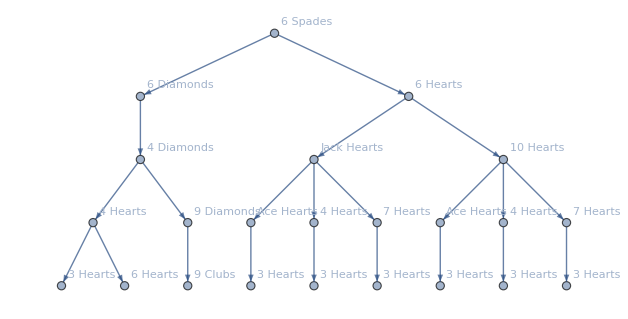

```mathematica
graph = GameTree[initialState, rules, 4];
PlotGameTree[graph]
```